The cross section dσ/dz and σ(s). z = cos θ and I have included the factor of 1/(2×2) for averaging over polarizations of protons and neutrons.

```mathematica
GeVtoBarn=0.3894*10^-3;
Barntocm2=10^-28(100)^2;
```

### p n → p n

```mathematica
dσdzPN[s_,ga_,fPi_,MNucleon_,MPi_,z_]:=1/4(ga^4*MNucleon^4*(4*MNucleon^2-s)^2*(48*MNucleon^4-48*MNucleon^2*MPi^2+12*MPi^4-24*MNucleon^2*s+12*MPi^2*s+3*s^2-48*MNucleon^2*MPi^2*z+24*MPi^4*z+12*MPi^2*s*z-96*MNucleon^4*z^2+48*MNucleon^2*MPi^2*z^2+28*MPi^4*z^2+48*MNucleon^2*s*z^2-12*MPi^2*s*z^2-6*s^2*z^2+48*MNucleon^2*MPi^2*z^3-12*MPi^2*s*z^3+48*MNucleon^4*z^4-24*MNucleon^2*s*z^4+3*s^2*z^4))/(8*fPi^4*Pi*s*(4*MNucleon^2-2*MPi^2-s+4*MNucleon^2*z-s*z)^2*(-4*MNucleon^2+2*MPi^2+s+4*MNucleon^2*z-s*z)^2);
totalXSEC[s_,ga_,fPi_,MNucleon_,MPi_]:=-1/16*(ga^4*MNucleon^4*(12*MNucleon^2-8*MPi^2-3*s)*((4*MNucleon^2-s)*(4*MNucleon^2-2*MPi^2-s)+2*MPi^2*(-4*MNucleon^2+MPi^2+s)*(2*Log[MPi]-Log[-4*MNucleon^2+MPi^2+s])))/(fPi^4*Pi*(4*MNucleon^2-s)*(4*MNucleon^2-2*MPi^2-s)*s*(-4*MNucleon^2+MPi^2+s))
```

```mathematica
Manipulate[Plot[dσdzPN[sqrts^2,ga,fPi,MNucleon,MPi,z]GeVtoBarn*10^3,{z,-1,1},PlotLabel->"dσ/(d  cosθ) for p n → p n scattering at √s = "<>ToString[Round[100sqrts]*0.01]<>"GeV",PlotRange->{All,All},Frame->True,FrameLabel->{"Center of mass scattering angle θ",Text["Cross section [ mb ]"]}],{MNucleon,0.98,10},{{sqrts,4MNucleon},2MNucleon,20},{{ga,1.25},-2,2},{{MPi,0.139},0,1},{{fPi,0.093},0,1}]
```

```mathematica
Manipulate[Plot[totalXSEC[sqrts^2,ga,fPi,MNucleon,MPi]GeVtoBarn*10^3,{sqrts,2MNucleon,10},PlotLabel->"σ_total for p n → p n scattering"<>"\n m_N = "<>ToString[Round[100MNucleon]*0.01]<>"GeV"<>" m_π = "<>ToString[Round[100MPi]*0.01]<>"GeV",PlotRange->All,Frame->True,AspectRatio->1,FrameLabel->{"√s [ GeV ]",Text["Cross section [ mb ]"]}],{MNucleon,0.98,10},{{ga,1.25},-2,2},{{MPi,0.139},0,1},{{fPi,0.093},0,1}]
```

```mathematica
Manipulate[Column@Sort@Flatten[Table[Ebeam/.FindRoot[totalXSEC[(2Ebeam)^2,ga,fPi,MNucleon,MPi]GeVtoBarn*10^3==target,{Ebeam,MNucleon*#}]&/@{1.01,1.1},{target,{10,20,30,40}}],1],{MNucleon,0.98,10},{{ga,1.25},-2,2},{{MPi,0.139},0,1},{{fPi,0.093},0,1}]
```

FindRoot::nlnum: 
   The function value {-10. + 1000. GeVtoBarn 
       totalXSEC[3.91882, 1.25, 0.093, 0.98, 0.139]} is not a list of numbers
     with dimensions {1} at {Ebeam} = {0.9898}.

ReplaceAll::reps: 
                                2
   {FindRoot[totalXSEC[(2 Ebeam) , FE`ga$$313, FE`fPi$$313, FE`MNucleon$$313, 
                                  3
         FE`MPi$$313] GeVtoBarn 10  == target, {Ebeam, FE`MNucleon$$313 1.01}]
      } is neither a list of replacement rules nor a valid dispatch table, and
     so cannot be used for replacing.

FindRoot::nlnum: 
   The function value {-10. + 1000. GeVtoBarn 
       totalXSEC[4.64834, 1.25, 0.093, 0.98, 0.139]} is not a list of numbers
     with dimensions {1} at {Ebeam} = {1.078}.

ReplaceAll::reps: 
                                2
   {FindRoot[totalXSEC[(2 Ebeam) , FE`ga$$313, FE`fPi$$313, FE`MNucleon$$313, 
                                  3
         FE`MPi$$313] GeVtoBarn 10  == target, {Ebeam, FE`MNucleon$$313 1.1}]}
     is neither a list of replacement rules nor a valid dispatch table, and so
     cannot be used for replacing.

FindRoot::nlnum: 
   The function value {-20. + 1000. GeVtoBarn 
       totalXSEC[3.91882, 1.25, 0.093, 0.98, 0.139]} is not a list of numbers
     with dimensions {1} at {Ebeam} = {0.9898}.

General::stop: Further output of FindRoot::nlnum
     will be suppressed during this calculation.

ReplaceAll::reps: 
                                2
   {FindRoot[totalXSEC[(2 Ebeam) , FE`ga$$313, FE`fPi$$313, FE`MNucleon$$313, 
                                  3
         FE`MPi$$313] GeVtoBarn 10  == target, {Ebeam, FE`MNucleon$$313 1.01}]
      } is neither a list of replacement rules nor a valid dispatch table, and
     so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps
     will be suppressed during this calculation.

```mathematica
Manipulate[Plot[{totalXSEC[(2Ebeam)^2,ga,fPi,MNucleon,MPi]GeVtoBarn*10^3,100,110,120},{Ebeam,MNucleon,1.3},PlotLabel->"σ_total for p n → p n scattering"<>"\n m_N = "<>ToString[Round[100MNucleon]*0.01]<>"GeV"<>" m_π = "<>ToString[Round[100MPi]*0.01]<>"GeV",PlotRange->All,Frame->True,AspectRatio->1,FrameLabel->{"Ebeam [ GeV ]",Text["Cross section [ mb ]"]}],{MNucleon,0.98,10},{{ga,1.25},-2,2},{{MPi,0.139},0,1},{{fPi,0.093},0,1}]
```

```mathematica
Manipulate[LogPlot[{totalXSEC[(2Ebeam)^2,ga,fPi,MNucleon,MPi]GeVtoBarn*10^9},{Ebeam,MNucleon,6500},PlotLabel->"σ_total for p n → p n scattering"<>"\n m_N = "<>ToString[Round[100MNucleon]*0.01]<>"GeV"<>" m_π = "<>ToString[Round[100MPi]*0.01]<>"GeV",PlotRange->All,Frame->True,AspectRatio->1,FrameLabel->{"Ebeam [ GeV ]",Text["Cross section [ mb ]"]}],{MNucleon,0.98,10},{{ga,1.25},-2,2},{{MPi,0.139},0,1},{{fPi,0.093},0,1}]
```

```mathematica
xseclist={3830,
1.255 10^11,
1.259 10^11,
1.262 10^11,
1.235 10^11,
1.225 10^11,
1.092 10^11,
9.966 10^11,
9.026 10^11,
3.579 10^10,
2.683 10^10,
1.793 10^10,
8.948 10^9}/10^12;
```

```mathematica
ebeamlist=Sqrt/@({n p
6500.0 x 6500.0 GeV
n p,
0.996955 x 0.996955 GeV
n p,
1.00286 x 1.00286 GeV
n p,
1.0132 x 1.0132 GeV
n p,
1.05265 x 1.05265 GeV
n p,
1.06046 x 1.06046 GeV
n p,
1.14829 x 1.14829 GeV
n p,
1.21409 x 1.21409 GeV
n p,
1.28322 x 1.28322 GeV
n p,
2.07372 x 2.07372 GeV
n p,
2.39976 x 2.39976 GeV
n p,
2.94508 x 2.94508 GeV
n p,
4.17318 x 4.17318 GeV
}/.{GeV->1,n->1,p->1,x->1});
```

```mathematica
datapoints=Transpose@{ebeamlist,xseclist};
```

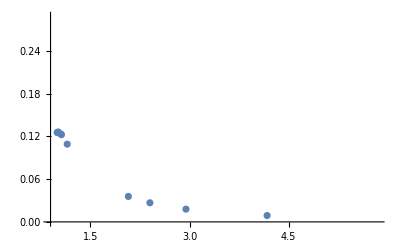

```mathematica
ListPlot[datapoints]
```

```mathematica
Manipulate[Plot[{totalXSEC[(2Ebeam)^2,ga,fPi,MNucleon,MPi]GeVtoBarn},{Ebeam,MNucleon,5},PlotLabel->"σ_total for p n → p n scattering"<>"\n m_N = "<>ToString[Round[100MNucleon]*0.01]<>"GeV"<>" m_π = "<>ToString[Round[100MPi]*0.01]<>"GeV",PlotRange->All,Frame->True,AspectRatio->1,FrameLabel->{"Ebeam [ GeV ]",Text["Cross section [ barn ]"]},Epilog->Point/@datapoints],{MNucleon,0.938272,10},{{ga,1.27},-2,2},{{MPi,0.1398},0,1},{{fPi,0.093},0,1}]
```

```mathematica
Manipulate[Plot[totalXSEC[(2 MNucleon^2+2MNucleon*(Ebeam+MNucleon)),ga,fPi,MNucleon,MPi]GeVtoBarn*10^3,{Ebeam,0,1},PlotLabel->"σ_total for p n → p n fixed target scattering"<>"\n m_N = "<>ToString[Round[100MNucleon]*0.01]<>"GeV"<>" m_π = "<>ToString[Round[100MPi]*0.01]<>"GeV",PlotRange->{{0,1},All},Frame->True,AspectRatio->1,FrameLabel->{"Ebeam [ GeV ]",Text["Cross section [ mb ]"]}],{MNucleon,0.98,10},{{ga,1.25},-2,2},{{MPi,0.139},0,1},{{fPi,0.093},0,1}]
```

### pπ^- → nπ^0

```mathematica
dσdz[e_,ga_,fPi_,sw_,MPi_,MW_,MNucleon_,s_,z_]:=2π((8*e^4*s*(-(MNucleon^6*(-1+z))+(1+ga^2)*(MPi^2-s)^2*s*(1+z)+MNucleon^4*(2*MPi^2*(-1+z)+s*(-1+3*z+ga^2*(1+z)))-MNucleon^2*(MPi^4*(-1+z)+2*MPi^2*s*(-2+ga^2*(1+z))+s^2*(1+3*z+2*ga^2*(1+z)))))/(sw^4*(s*(-2*MW^2+s*(-1+z))+MNucleon^4*(-1+z)+MPi^4*(-1+z)-2*MPi^2*s*(-1+z)-2*MNucleon^2*(MPi^2+s)*(-1+z))^2)+(16*e^2*(MNucleon^6*(-1+z)-(MPi^2-s)^2*s*(1+z)+MNucleon^4*(s-2*MPi^2*(-1+z)-3*s*z)+MNucleon^2*(-4*MPi^2*s+MPi^4*(-1+z)+s^2*(1+3*z)))*((1+ga^2)*MNucleon^6*(-1+z)+MNucleon^4*(s-ga^2*s*(-3+z)-2*(1+ga^2)*MPi^2*(-1+z)-3*s*z)+(-1+ga^2)*s*(MPi^4*(-1+z)-2*MPi^2*s*(1+z)+s^2*(1+z))+MNucleon^2*((1+ga^2)*MPi^4*(-1+z)-4*MPi^2*(s+ga^2*s*z)+s^2*(1+3*z-ga^2*(3+z)))))/(fPi^2*(MNucleon^2-s)*sw^2*(s*(-2*MW^2+s*(-1+z))+MNucleon^4*(-1+z)+MPi^4*(-1+z)-2*MPi^2*s*(-1+z)-2*MNucleon^2*(MPi^2+s)*(-1+z))*(MNucleon^4*(-1+z)+MPi^4*(-1+z)-2*MPi^2*s*(1+z)+s^2*(1+z)-2*MNucleon^2*(MPi^2*(-1+z)+s*z)))-(8*(MNucleon^6*(-1+z)-(MPi^2-s)^2*s*(1+z)+MNucleon^4*(s-2*MPi^2*(-1+z)-3*s*z)+MNucleon^2*(-4*MPi^2*s+MPi^4*(-1+z)+s^2*(1+3*z)))*((1+ga^2)*MNucleon^6*(-1+z)+MNucleon^4*(s-ga^2*s*(-3+z)-2*(1+ga^2)*MPi^2*(-1+z)-3*s*z)+(-1+ga^2)*s*(MPi^4*(-1+z)-2*MPi^2*s*(1+z)+s^2*(1+z))+MNucleon^2*((1+ga^2)*MPi^4*(-1+z)-4*MPi^2*(s+ga^2*s*z)+s^2*(1+3*z-ga^2*(3+z))))^2)/(fPi^4*(MNucleon^2-s)^2*s*(MNucleon^4*(-1+z)+MPi^4*(-1+z)-2*MPi^2*s*(1+z)+s^2*(1+z)-2*MNucleon^2*(MPi^2*(-1+z)+s*z))^2))/(2048*Pi^2*s)
```

```mathematica
TotalCrossSection[e_,ga_,fPi_,sw_,MPi_,MW_,MNucleon_,s_]:=(((MNucleon-MPi)^2-s)*((MNucleon+MPi)^2-s)*((1+ga^2)^2*MNucleon^6*(MNucleon^2-MPi^2)^4*(MNucleon^2+2*MPi^2)-(1+ga^2)*MNucleon^4*(MNucleon-MPi)^2*(MNucleon+MPi)^2*((5+9*ga^2)*MNucleon^6+2*(-1+7*ga^2)*MNucleon^4*MPi^2-2*(7+ga^2)*MNucleon^2*MPi^4+2*(1-3*ga^2)*MPi^6)*s+MNucleon^2*(3*(3+7*ga^2*(2+ga^2))*MNucleon^10+2*(-15-10*ga^2+ga^4)*MNucleon^8*MPi^2-(1+54*ga^2+5*ga^4)*MNucleon^6*MPi^4+32*(1+ga^2)*MNucleon^4*MPi^6-4*(5-ga^2+ga^4)*MNucleon^2*MPi^8+2*(-1-2*ga^2+3*ga^4)*MPi^10)*s^2-((5+70*ga^2+13*ga^4)*MNucleon^10+8*(-5+ga^4)*MNucleon^8*MPi^2+2*(3-22*ga^2+21*ga^4)*MNucleon^6*MPi^4-8*(-1-2*ga^2+ga^4)*MNucleon^4*MPi^6+2*(-7+4*ga^2+3*ga^4)*MNucleon^2*MPi^8-2*(-1+ga^2)^2*MPi^10)*s^3+((-5+70*ga^2-13*ga^4)*MNucleon^8+2*(-15+10*ga^2+ga^4)*MNucleon^6*MPi^2+4*(1-2*ga^2+6*ga^4)*MNucleon^4*MPi^4-8*(-1+ga^2)^2*MNucleon^2*MPi^6-5*(-1+ga^2)^2*MPi^8)*s^4+(3*(3+7*ga^2*(-2+ga^2))*MNucleon^6+4*(3-4*ga^2+ga^4)*MNucleon^4*MPi^2+(1-6*ga^2+5*ga^4)*MNucleon^2*MPi^4+4*(-1+ga^2)^2*MPi^6)*s^5-(-1+ga^2)*((-5+9*ga^2)*MNucleon^4+2*(-1+ga^2)*MNucleon^2*MPi^2+(-1+ga^2)*MPi^4)*s^6+(-1+ga^2)^2*MNucleon^2*s^7)-8*ga^2*MNucleon^2*(MNucleon^2-s)*(MNucleon^2+2*MPi^2-s)*s^2*(MNucleon^4+MPi^4-MNucleon^2*(2*MPi^2+s))*(MPi^4*(-MNucleon^2+s)+ga^2*(MNucleon^6-2*MNucleon^4*s-MPi^4*s+MNucleon^2*(-MPi^4+s^2)))*Log[((MNucleon^2+2*MPi^2-s)*s)/(MNucleon^4+MPi^4-MNucleon^2*(2*MPi^2+s))])/(64*fPi^4*Pi*(MNucleon^2-s)^2*(MNucleon^2+2*MPi^2-s)*s^2*(MNucleon^4+(MPi^2-s)^2-2*MNucleon^2*(MPi^2+s))*(MNucleon^4+MPi^4-MNucleon^2*(2*MPi^2+s)))
```

```mathematica
Manipulate[Plot[dσdz[√(4π α),ga,fPi,sw,MPi,MW,MNucleon,sqrts^2,z]GeVtoBarn*10^3,{z,-1,1},PlotLabel->"dσ/(d  cosθ) for p π^- → n π^0 scattering at √s = "<>ToString[Round[100sqrts]*0.01]<>"GeV",PlotRange->{All,All},Frame->True,FrameLabel->{"z = cos θ",Text["Cross section [ mb ]"]}],{MNucleon,0.98,10},{{MW,81},1,100},{{sqrts,2MNucleon},MNucleon+MPi,10},{{α,1/137.0},0,1},{{ga,1.27},-2,2},{{sw,0.5},0,1},{{MPi,0.139},0,1},{{fPi,0.13},0,1}]
```

```mathematica
Manipulate[Plot[TotalCrossSection[√(4π α),ga,fPi,sw,MPi,MW,MNucleon,sqrts^2]GeVtoBarn*10^3,{sqrts,MNucleon+MPi,5},PlotLabel->"σ_total for π^- p → π^0 n fixed target scattering"<>"\n m_N = "<>ToString[Round[100MNucleon]*0.01]<>"GeV"<>" m_π = "<>ToString[Round[100MPi]*0.01]<>"GeV",PlotRange->All,Frame->True,AspectRatio->1,FrameLabel->{"E_(π  beam) [ GeV ]",Text["Cross section [ mb ]"]}],{MNucleon,0.98,10},{{MW,81},1,100},{{α,1/137.0},0,1},{{ga,1.27},-2,2},{{sw,0.5},0,1},{{MPi,0.139},0,1},{{fPi,0.13},0,1}]
```

```mathematica
Manipulate[Plot[{TotalCrossSection[√(4π α),ga,fPi,sw,MPi,MW,MNucleon,(MNucleon^2+MPi^2+2MNucleon*(Ebeam+MPi))^2]GeVtoBarn*10^3,TotalCrossSectionNonUnitaryPiece[√(4π α),ga,fPi,sw,MPi,MW,MNucleon,(MNucleon^2+MPi^2+2MNucleon*(Ebeam+MPi))^2]GeVtoBarn*10^3,TotalCrossSection[√(4π α),ga,fPi,sw,MPi,MW,MNucleon,(MNucleon^2+MPi^2+2MNucleon*(Ebeam+MPi))^2]GeVtoBarn*10^3-TotalCrossSectionNonUnitaryPiece[√(4π α),ga,fPi,sw,MPi,MW,MNucleon,(MNucleon^2+MPi^2+2MNucleon*(Ebeam+MPi))^2]GeVtoBarn*10^3},{Ebeam,0,1},PlotLabel->"σ_total for π^- p → π^0 n fixed target scattering"<>"\n m_N = "<>ToString[Round[100MNucleon]*0.01]<>"GeV"<>" m_π = "<>ToString[Round[100MPi]*0.01]<>"GeV",PlotRange->All,Frame->True,AspectRatio->1,FrameLabel->{"E_(π  beam) [ GeV ]",Text["Cross section [ mb ]"]},PlotLegends->{"Total Cross Section","The nonunitary piece","Total minus nonunitary"}],{MNucleon,0.98,10},{{MW,81},1,100},{{α,1/137.0},0,1},{{ga,1.27},-2,2},{{sw,0.5},0,1},{{MPi,0.139},0,1},{{fPi,0.13},0,1}]
```

```mathematica
Series[TotalCrossSection[e,ga,fPi,sw,MPi,MW,MNucleon,s],{s,∞,0}]
```

((-1+ga^2)^2 s)/(64 fPi^4 π)+(-MNucleon^2+6 ga^2 MNucleon^2-5 ga^4 MNucleon^2-2 MPi^2+4 ga^2 MPi^2-2 ga^4 MPi^2)/(64 fPi^4 π)+O[1/s]^1

```mathematica
TotalCrossSectionNonUnitaryPiece[e_,ga_,fPi_,sw_,MPi_,MW_,MNucleon_,s_]:=((-1+ga^2)^2 s)/(64 fPi^4 π);
```